# emission from a dipole

```mathematica
Clear[k]
conj[z_]:=z/.{ⅈ-> -ⅈ,-ⅈ->ⅈ};
(*Green's tensor for dipole emission along r hat dotted with polarization vector p hat*)
GdotP[r_,p_]:=ⅇ^(ⅈ k √(r.r))/(4 π √(r.r))(Cross[Cross[unit[r],p],unit[r]]+(1/(k^2 r.r)-ⅈ/(k √(r.r)))(3unit[r] Dot[unit[r],p]-p));
```

```mathematica
pz = {Cos[θ],-Sin[θ],0};
r = {1,0,0};
```

```mathematica
Dot[GdotP[r,pz],conj[GdotP[r,pz]]]
```

```mathematica
((1/k^2-ⅈ/k)^2 Cos[θ]^2)/(4 π^2)+((-Sin[θ]+(1/k^2-ⅈ/k) Sin[θ])^2)/(16 π^2)
```

## photon states

spherical basis r, θ, ϕ. From LJ Stephenson thesis:

```mathematica
pi ={0,-Sin[θ],0};
rh =ⅇ^(ⅈ ϕ)/(√2){0,Cos[θ],ⅈ};
lh = ⅇ^(-ⅈ ϕ)/(√2){0,Cos[θ],-ⅈ};
```

```mathematica
Map[#.#&,{pi,rh,lh}]
```

{Sin[θ]^2,-1/2 ⅇ^(2 ⅈ ϕ)+1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^2,-1/2 ⅇ^(-2 ⅈ ϕ)+1/2 ⅇ^(-2 ⅈ ϕ) Cos[θ]^2}

```mathematica
{0,ⅈ}.conj[{0,ⅈ}]
```

1

```mathematica
lh
```

{0,(ⅇ^(-ⅈ ϕ) Cos[θ])/(√2),-(ⅈ ⅇ^(-ⅈ ϕ))/(√2)}

```mathematica
conj[lh]
```

{0,(ⅇ^(ⅈ ϕ) Cos[θ])/(√2),(ⅈ ⅇ^(ⅈ ϕ))/(√2)}

Verify that the three states give equal contribution of polarization

```mathematica
Map[Integrate[#.conj[#] Sin[θ],{θ,0,π},{ϕ,0,2π}]&,{pi,lh,rh}]
```

{(8 π)/3,(8 π)/3,(8 π)/3}

Verify the states are orthogonal

```mathematica
Integrate[rh.conj[pi] Sin[θ],{θ,0,π},{ϕ,0,2π}]
Integrate[lh.conj[pi] Sin[θ],{θ,0,π},{ϕ,0,2π}]
Integrate[lh.conj[rh] Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

0

0

0

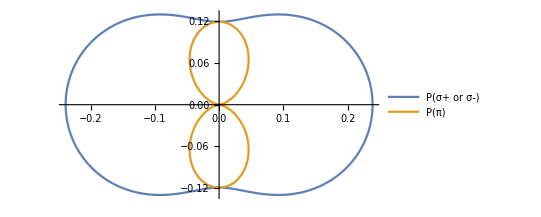

```mathematica
PolarPlot[{(lh.conj[lh]+rh.conj[rh])3/(8π),pi.conj[pi] 3/(8π)},{θ,0,2π},PlotLegends->{"P(σ+ or σ-)","P(π)"}]
```